```mathematica
Afina preslikavanja
```

```mathematica
Marija Kostic 286/14
```

```mathematica
Neka je A matrica, a v vektor koji odredjuju afino preslikavanje tacke x.
```

```mathematica
AfinoPreslikavanje[A_,v_][x_]:=A.x+v;
```

```mathematica
Definišemo matrice rotacije,skaliranja i smicanja.
```

```mathematica
Rotacija[ϕ_]:=({{Cos[ϕ], -Sin[ϕ]}, {Sin[ϕ], Cos[ϕ]}});
```

```mathematica
Skaliranje[a_,b_]:=({{a, 0}, {0, b}});
```

```mathematica
Smicanje[λ_]:=({{1, λ}, {0, 1}});
```

```mathematica
Pravimo poligon zvezda tako što zadajemo koordinate temena.
```

```mathematica
Zvezda={{0,0},{1.5,1.09},{3,0},{2.43,1.76},{3.92,2.85},{2.07,2.85},{1.51,4.62},{0.93,2.85},{-0.92,2.85},{0.57,1.76}};
```

```mathematica
Definišemo funkciju za preslikavanje poligona.
```

```mathematica
AfinoPreslikavanje[A_,v_][p_Polygon]:=Polygon[AfinoPreslikavanje[A,v][#]&/@(p[[1]])];
```

```mathematica
Original=Polygon[Zvezda];
```

```mathematica
Pravimo sliku originalnog poligona i poligona posle rotacije,smicanja i translacije.
```

```mathematica
Slika=AfinoPreslikavanje[Rotacija[Pi/6].Smicanje[1],{3,4}][Polygon[Zvezda]];
```

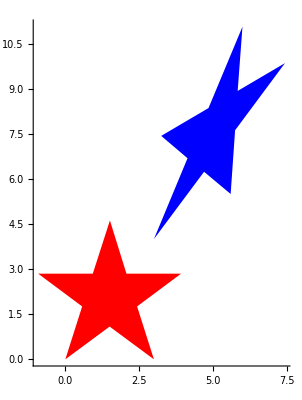

```mathematica
Show[Graphics[{Red,Original}],Graphics[{Blue,Slika}],Axes->True]
```

```mathematica
Odredjujemo matricu transformacije.
```

```mathematica
AfinoPreslikavanje[Rotacija[Pi/6].Smicanje[1],{3,4}][[1]]//MatrixForm
```

((√3)/2 | -1/2+(√3)/2
1/2 | 1/2+(√3)/2)

```mathematica
Odredjujemo i vektor transformacije.
```

```mathematica
AfinoPreslikavanje[Rotacija[Pi/6].Smicanje[1],{3,4}][[2]]//MatrixForm
```

(3
4)

```mathematica
Pravimo sliku pri komutiranoj transformaciji.
```

```mathematica
Slika2=AfinoPreslikavanje[Smicanje[1].Rotacija[Pi/6],{3,4}][Polygon[Zvezda]];
```

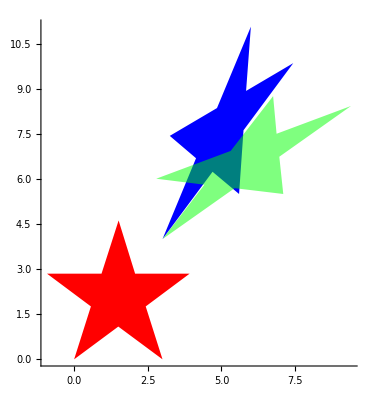

```mathematica
Show[Graphics[{Red,Original}],Graphics[{Blue,Slika}],Graphics[{Green,Opacity[0.5],Slika2}],Axes->True]
```

```mathematica
Odredjujemo matricu transformacije.
```

```mathematica
AfinoPreslikavanje[Smicanje[1].Rotacija[Pi/6],{3,4}][[1]]//MatrixForm
```

(1/2+(√3)/2 | -1/2+(√3)/2
1/2 | (√3)/2)

```mathematica
Odredjujemo i vektor transformacije.
```

```mathematica
AfinoPreslikavanje[Smicanje[1].Rotacija[Pi/6],{3,4}][[2]]//MatrixForm
```

(3
4)

```mathematica
Primecujemo da množenje matrica ne komutira.
```